```mathematica
eta1=1.2;
eta2=1.1;
eta3=1.3;
eta4=0.5;
```

```mathematica
Eq129[Q_,eta_]:=Exp[-Q^2/(4*eta^2)]
```

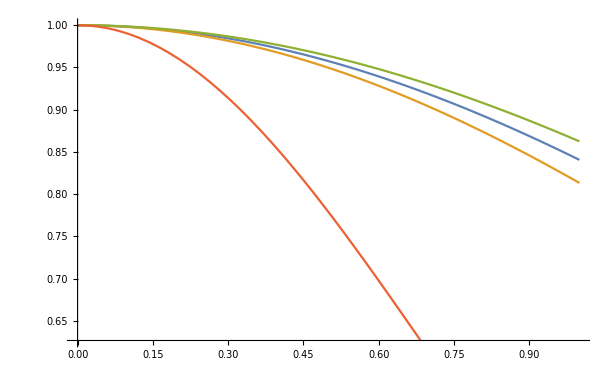

```mathematica
Plot[{Eq129[Q,eta1],Eq129[Q,eta2],Eq129[Q,eta3],Eq129[Q,eta4]},{Q,0,1}]
```

```mathematica
Eq130[R_,eta_]:=Erfc[R*eta]/R^3
```

```mathematica
const=100;
```

```mathematica
Eq3[R_,eta_]:=Exp[-R^2 eta^2]eta*(3+const)/R^2
```

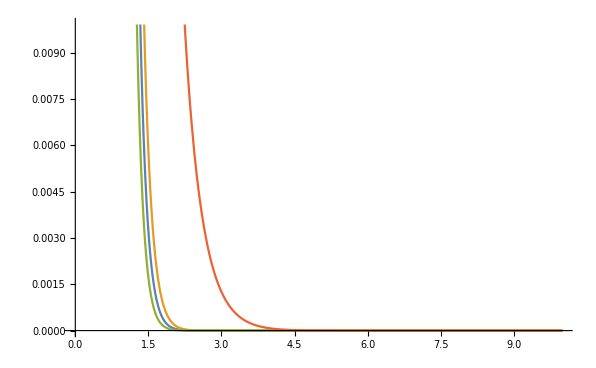

```mathematica
Plot[{Eq130[R,eta1],Eq130[R,eta2],Eq130[R,eta3],Eq130[R,eta4]},{R,0,10}]
```

L18 varies between 3.97 and 11
L12 varies between 12 and 40
L2 varies between 30 and 120

The length of the reciprocal lattice vector might be even lower than 3.97. Will look at how its actually calculated and figure it out. I just did a quick test by printing the lattice vector lengths. 

So the length of the reciprocal lattice vector (if sufficiently below 3.97) for eta=0.5 is not quite large enough? The calculation is being cutoff too soon? 

Does this mean the ogg state is the ground state?